```mathematica
(*Styling of the text*)st[text_]:=Style[text,Directive[FontSize->20,FontFamily->"Linux Libertine Display"]];
(*Styling of the ticks*)

ticksstyle=Directive[FontSize->20,FontFamily->"Linux Libertine Display"];
(*Styling of the frame*)

framestyle=Directive[FontSize->15,FontFamily->"Linux Libertine Display"];
```

### Definitions

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
rot=28; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

hf[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with e^ik bc *)
hn[k_,n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw Exp[I k]];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Harper *)
hharp[p_,q_,ϕ_,λ_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.λ Cos[2 π p i/q+ϕ],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_,ϕ_,λ_]:=hharp[Fibonacci[n-1],Fibonacci[n],ϕ,λ];
SetAttributes[hfib,Listable];
```

### Plot conumbering

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
intp=Block[{val,vec,n=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hk[0,n,tw,ts]];
(*order wavefunctions by increasing energy*)
Abs[vec[[Ordering[val]]]]^2
];
```

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
inta=Block[{val,vec,n=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hk[Pi,n,tw,ts]];
(*order wavefunctions by increasing energy*)
Abs[vec[[Ordering[val]]]]^2
];
```

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
inthalf=Block[{val,vec,n=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hk[Pi/2,n,tw,ts]];
(*order wavefunctions by increasing energy*)
Abs[vec[[Ordering[val]]]]^2
];
```

```mathematica
meanint=(intp+4 inthalf+inta)/6;
```

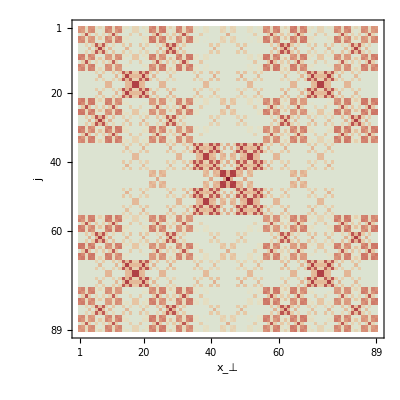

```mathematica
(* we replace intensities below the threshold by 0 *) 
threshold=10^-2;
(* color of the thresholded points *)
(*colorThreshold=White;*)
colorThreshold=ColorData["ThermometerColors",0.5];
(* max amplitude *)
M=Max[√meanint];
plot=MatrixPlot [Threshold[meanint^(1/3),{"Hard","Median"}],FrameLabel->st/@{"j","x_⊥"},ColorFunction->"ThermometerColors",ColorRules->{0->colorThreshold},FrameStyle->framestyle];
bl=BarLegend[{ColorData["ThermometerColors",(0.5#+0.5)]&,{0,1}},LegendLabel->"LDoS"];
plot
```

```mathematica
Export[NotebookDirectory[]<>"ldos_reordered_conumbering.pdf",%]
```

/home/nicolas/git/talks/ICQ13 September 2016/talk/img/ldos_reordered_conumbering.pdf

### Plot normal numbering

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
intp=Block[{val,vec,n=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hn[0,n,tw,ts]];
(*order wavefunctions by increasing energy*)
Abs[vec[[Ordering[val]]]]^2
];
```

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
inta=Block[{val,vec,n=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hn[Pi,n,tw,ts]];
(*order wavefunctions by increasing energy*)
Abs[vec[[Ordering[val]]]]^2
];
```

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
inthalf=Block[{val,vec,n=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hn[Pi/2,n,tw,ts]];
(*order wavefunctions by increasing energy*)
Abs[vec[[Ordering[val]]]]^2
];
```

```mathematica
meanint=(intp+4 inthalf+inta)/6;
(* reorder wavefunction by conumber *)
co[l_,i_]:=Mod[(i-rot) Fibonacci[l-1],Fibonacci[l],1];
l=9+2;
meanint=Table[meanint[[co[l,i]]],{i,Fibonacci[l]}];
```

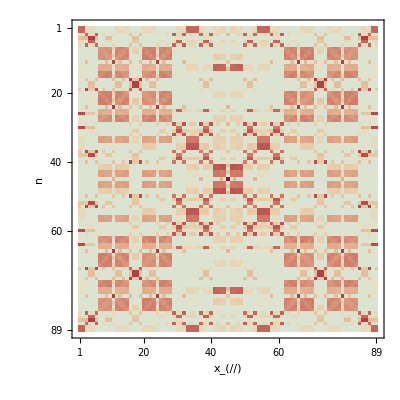

```mathematica
(* we replace intensities below the threshold by 0 *) 
threshold=10^-2;
(* color of the thresholded points *)
(*colorThreshold=White;*)
colorThreshold=ColorData["ThermometerColors",0.5];
(* max amplitude *)
M=Max[√meanint];
plot=MatrixPlot [Threshold[meanint^(1/3),{"Hard","Median"}],FrameLabel->st/@{"n","x_(//)"},ColorFunction->"ThermometerColors",ColorRules->{0->colorThreshold},FrameStyle->framestyle];
bl=BarLegend[{ColorData["ThermometerColors",(0.5#+0.5)]&,{0,1}},LegendLabel->"LDoS"];
plot
```

```mathematica
Export[NotebookDirectory[]<>"ldos_reordered_numbering.pdf",%]
```

/home/nicolas/git/talks/ICQ13 September 2016/talk/img/ldos_reordered_numbering.pdf